# Nonlinear Dynamical Systems Assignment 3 - Notebook.

## Tiger Bush Stripes - Spatial Patterns - Turning Mechanism. By James Zoryk.

## Notes for Assignment.

### Question 1.

Here we are given the system of PDEs which we can solve and evaluate.

```mathematica
eq1[v_, w_, γ_ , Dxx_ ]:= Dxx v - γ v + w v^2;
eq2[v_, w_,α_,β_, γ_ , Dx_ ]:= β Dx w +α- w - w v^2;
```

Setting Dxx and Dx both to zero and solving yields

```mathematica
pdeS1 =Solve[{ eq1[v,w,γ,0]==0, eq2[v,w,α, β,γ, 0]==0},{v,w}] // MatrixForm
```

(v→0 | w→α
v→(α-√(α^2-4 γ^2))/(2 γ) | w→1/2 (α+√(α^2-4 γ^2))
v→(α+√(α^2-4 γ^2))/(2 γ) | w→1/2 (α-√(α^2-4 γ^2)))

This gives us the three equilibrium.  If α < 2 γ then only one:
 - Which is the equilibrium for no vegetation. 
If α > 2 γ then we have 3:

Here we create a function to compute the Jacobian .

```mathematica
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
eqsJacobian [v_, w_,α_,β_, γ_ ]:=JacobianMatrix[{ eq1[v,w,γ,0], eq2[v,w,α, β,γ, 0]},{v,w}];
```

```mathematica
jacobianMatrix =eqsJacobian[v,w,α, β,γ] ;
jacobianMatrix // MatrixForm
```

(2 v w-γ | v^2
-2 v w | -1-v^2)

For   we have the following Jacobian Matrix

```mathematica
e2JacobianM = Simplify [jacobianMatrix /. { pdeS1[[1]][[2]][[1]] , pdeS1[[1]][[2]][[2]]}];
e2JacobianM  //MatrixForm
e2JMDet[α_, γ_]:=Det[ e2JacobianM];
e2JMDet[α, γ]
```

(γ | ((α-√(α^2-4 γ^2))^2)/(4 γ^2)
-2 γ | (α (-α+√(α^2-4 γ^2)))/(2 γ^2))

α^2/(2 γ)-2 γ-(α √(α^2-4 γ^2))/(2 γ)

For  we have the following Jacobian Matrix

```mathematica
e3JacobianM = Simplify [jacobianMatrix /. { pdeS1[[1]][[3]][[1]] , pdeS1[[1]][[3]][[2]]}];
e3JacobianM  //MatrixForm
e3JMDet[α_, γ_]:=Det[ e3JacobianM];
e3JMDet[α, γ]
e3JMTr = Tr[e3JacobianM]
```

(γ | ((α+√(α^2-4 γ^2))^2)/(4 γ^2)
-2 γ | -(α (α+√(α^2-4 γ^2)))/(2 γ^2))

α^2/(2 γ)-2 γ+(α √(α^2-4 γ^2))/(2 γ)

γ-(α (α+√(α^2-4 γ^2)))/(2 γ^2)

```mathematica
Plot3D[ {e2JMDet[α, γ],e3JMDet[α, γ]}, { α, 0, 10},{ γ, 0, 5},PlotLegends->"Expressions", AxesLabel->{α, γ, z}]
```

-Graphics3D-

Here we compute the trace of the Jacobian since this tells us about the stability of the point.

```mathematica
se3Tr =Solve[e3JMTr==0, α]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{α→-γ^2/(√(-1+γ))},{α→γ^2/(√(-1+γ))}}

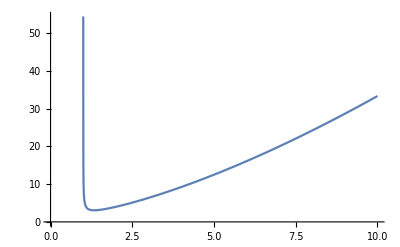

```mathematica
Plot[ α  /.se3Tr[[2]], {γ, 0, 10}]
```

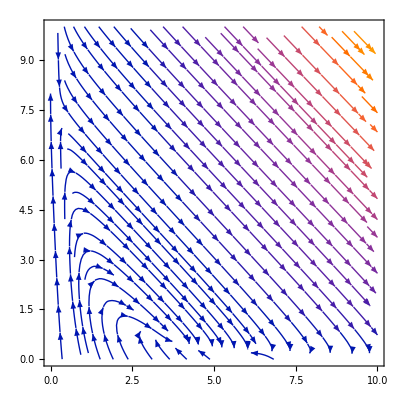

```mathematica
StreamPlot[{eq1[v, w, 2 ,0 ], eq2[v, w,8,20, 2 ,0 ]}, {v, 0,10},{w,0,10}]
```

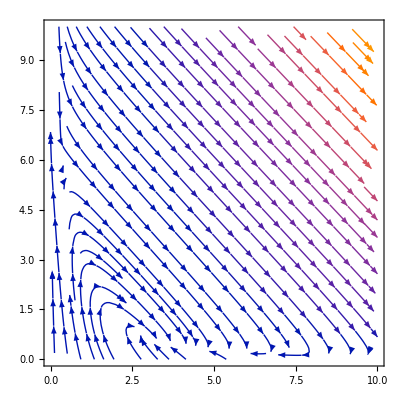

```mathematica
StreamPlot[{eq1[v, w, 2 ,0 ], eq2[v, w,7,20, 2 ,0 ]}, {v, 0,10},{w,0,10}]
```